#### Hometask 1. Multi-criteria tasks

Compromise solution

```mathematica
f1[x1_,x2_]:=-x1+x2-6
f2[x1_,x2_]:=x1+x2+2
```

```mathematica
minf1=FindMinimum[{f1[x1,x2],13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{-10.,{x1→4.,x2→0.}}

```mathematica
maxf2=FindMaximum[{f2[x1,x2],13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{7.,{x1→4.,x2→1.}}

Identify a compromise variable

```mathematica
fGen[x1_,x2_,x3_]:=x3
```

(7-(x_1+x_2+2))/7≤x_3
(-x_1+x_2-6+10)/-10≤x_3
x_3→min

```mathematica
solution1=FindMinimum[{fGen[x1,x2,x3],{x1,x2,x3}.{1,1,maxf2⟦1⟧}+2≥maxf2⟦1⟧&&{x1,x2,x3}.{-1,1,minf1⟦1⟧}-6≤minf1⟦1⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2&&x3≥0},{x1,x2,x3}]
```

{0.0588235,{x1→4.,x2→0.588235,x3→0.0588235}}

```mathematica
{f1[solution1⟦2,1⟧//Values,solution1⟦2,2⟧//Values],f2[solution1⟦2,1⟧//Values,solution1⟦2,2⟧//Values]}
```

{-9.41176,6.58824}

Main criteria

```mathematica
concs=0.1;
```

(x_1+x_2+2-7)/7≤p_1

```mathematica
δ1=maxf2⟦1⟧*concs
```

0.7

```mathematica
solution2=FindMinimum[{f1[x1,x2],f2[x1,x2]≥(maxf2⟦1⟧-concs*maxf2⟦1⟧)&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{-9.7,{x1→4.,x2→0.3}}

```mathematica
{f1[solution2⟦2,1⟧//Values,solution2⟦2,2⟧//Values],f2[solution2⟦2,1⟧//Values,solution2⟦2,2⟧//Values]}
```

{-9.7,6.3}

Two criteria

```mathematica
concs1={0.05,0.1,0.15}*minf1⟦1⟧;
concs2={0.1,0.15,0.2}*maxf2⟦1⟧;
```

```mathematica
FindMinimum[{f1[x1,x2],f2[x1,x2]≤maxf2⟦1⟧+concs2⟦1⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{-10.,{x1→4.,x2→0.}}

```mathematica
FindMinimum[{f1[x1,x2],f2[x1,x2]≤maxf2⟦1⟧+concs2⟦2⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{-10.,{x1→4.,x2→0.}}

```mathematica
FindMinimum[{f1[x1,x2],f2[x1,x2]≤maxf2⟦1⟧+concs2⟦3⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{-10.,{x1→4.,x2→0.}}

```mathematica
FindMaximum[{f2[x1,x2],f1[x1,x2]≥minf1⟦1⟧+concs1⟦1⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{7.,{x1→4.,x2→1.}}

```mathematica
FindMaximum[{f2[x1,x2],f1[x1,x2]≥minf1⟦1⟧+concs1⟦2⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{7.,{x1→4.,x2→1.}}

```mathematica
FindMaximum[{f2[x1,x2],f1[x1,x2]≥minf1⟦1⟧+concs1⟦3⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{7.,{x1→4.,x2→1.}}

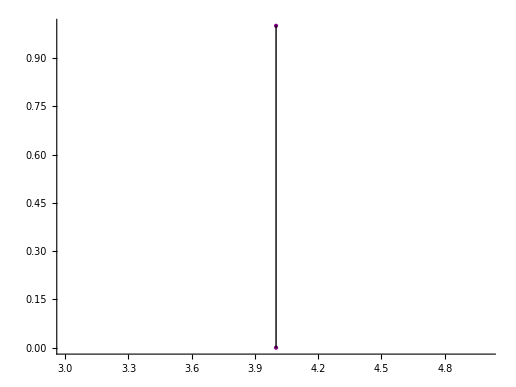

```mathematica
Graphics[{Purple,PointSize[Large],Point[{4,0}],Point[{4,1}],Black,Line[{{4,0},{4,1}}]},Axes->True]
```

```mathematica
{f1[4,1],f2[4,1]}
```

{-9,7}

Equal Variation

-x_1+x_2-6-f_1=0
x_1+x_2+2-f_2=0
f2/(f_(2,max))+(-x_1+x_2-6)/(f_(1,min))=2

```mathematica
solution4=FindMaximum[{f2[x1,x2],fe2/7+f1[x1,x2]/-10== 2&&f1[x1,x2]-fe1==0&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2,fe1,fe2}]
```

{7.,{x1→4.,x2→1.,fe1→-9.,fe2→7.7}}

```mathematica
{f1[solution4⟦2,1⟧//Values,solution3⟦2,2⟧//Values],f2[solution4⟦2,1⟧//Values,solution3⟦2,2⟧//Values]}
```

{-9.,7.}

Expert evaluations

```mathematica
alpha={0.2,0.8};
```

```mathematica
fGen2[x1_,x2_]:=alpha⟦1⟧*f1[x1,x2]/minf1⟦1⟧+alpha⟦2⟧*f2[x1,x2]/maxf2⟦1⟧
```

```mathematica
solution3=FindMaximum[{fGen2[x1,x2],13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{0.98,{x1→4.,x2→1.}}

```mathematica
{f1[solution3⟦2,1⟧//Values,solution3⟦2,2⟧//Values],f2[solution3⟦2,1⟧//Values,solution3⟦2,2⟧//Values]}
```

{-9.,7.}

Solutions

```mathematica
Grid[{{"Compromise solution","Main criteria","Two criteria","Equal variation","Expert evaluations"},{{-9.41,6.58},{-9.7,6.3},{-9,7},{-9,7},{-9,7}}},Frame->All,Background->{None,{RGBColor["#bc84f0"]}},ItemSize->{11,2}]
```

Compromise solution | Main criteria | Two criteria | Equal variation | Expert evaluations
{-9.41,6.58} | {-9.7,6.3} | {-9,7} | {-9,7} | {-9,7}